```mathematica
f[x_]:=Log[2-x-5x^2]
f'[x]
```

(-1-10 x)/(2-x-5 x^2)

```mathematica
f[x_]:=Log[Abs[x]]
f'[x]
```

Abs'[x]/Abs[x]

```mathematica
Abs'[x]
```

Abs'[x]

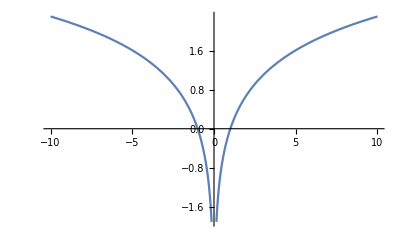

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
Clear[f]
```

```mathematica
f[x_]:=1/2 Log[(a^2-x^2)/(a^2+x^2)]
D[Log[a^2-x^2],x]
Simplify[f[z]]
f'[z]//Simplify
```

-(2 x)/(a^2-x^2)

1/2 Log[(a^2-z^2)/(a^2+z^2)]

-(2 a^2 z)/(a^4-z^4)

```mathematica
f[x_]:=x/(1-Log[x-1])
f'[x]
```

x/((-1+x) (1-Log[-1+x])^2)+1/(1-Log[-1+x])

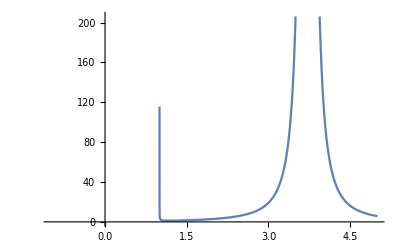

x+2 x Log[2 x]

3+2 Log[2 x]

```mathematica
Plot[x/((-1+x) (1-Log[-1+x])^2)+1/(1-Log[-1+x]),{x,-1,5.}]
```

```mathematica
Sec'[x]
```

Sec[x] Tan[x]

```mathematica
Log[0]
```

-∞

```mathematica
ClearAll[x,y,f]
f[x]:=x^2+y^2
D[y[x]]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[x^2]

```mathematica
ContourPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]
```

ContourPlot::pllim: Range specification {} ⟦ 1 ⟧ is not of the form {x, xmin, xmax}.

ContourPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]

```mathematica
DensityPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]
```

RegionPlot::pllim: Range specification {} ⟦ 1 ⟧ is not of the form {x, xmin, xmax}.

DensityPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]

```mathematica
ContourPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]
```

ContourPlot::pllim: Range specification {} ⟦ 1 ⟧ is not of the form {x, xmin, xmax}.

ContourPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]

```mathematica
Solve[y'==(2x+2y y')/(x^2+y^2),y']
```

{{y'→(2 x)/(x^2-2 y+y^2)}}

```mathematica
a[t_]:= x[t]^2
Dt[a[t],t]
%/.{x[t]->4, x'[t]->6}
%//N
```

2 x[t] x'[t]

48

48.

```mathematica
v[t_]:=Pi 
Dt[a[t],t]
%/.{x[t]->20 cm,y[t]->10 cm,x'[t]->8 cm/s,y'[t]->3 cm/s}
```

y[t] x'[t]+x[t] y'[t]

(140 cm^2)/s

```mathematica
v[t_]:=4/3 π r[t ]^3
Dt[v[t],t]
%/.{r[t]->40mm,r'[t]->4mm/s}
% * (1 cm^3)/(1000 mm^3)//N
```

4 π r[t]^2 r'[t]

(25600 mm^3 π)/s

(80.4248 cm^3)/s

```mathematica
4 π r[t]^2 r'[t]
```

12.5664 r[t]^2 r'[t]

```mathematica
150-35 4
```

10

```mathematica
r[t_]:=Sqrt[90^2+x[t]^2]
Dt[r[t],t]//Simplify
%/.{x'[t]->24,x[t]->45}//N
```

(x[t] x'[t])/(√(8100+x[t]^2))

10.7331

```mathematica
Clear[x,y]
```

```mathematica
x[t_]=.
```

Unset::norep: Assignment on x for x[t_] not found.

$Failed

```mathematica
x
```

x

```mathematica
y
```

y

```mathematica
r[t_]:=Sqrt[60^2+25^2]t
r[t]
r'[t]
```

65 t

65

```mathematica
f[t_]:=(60 60t)/Sqrt[100^2+(60t)^2]
f[t]//Simplify
f[4]
%//N
```

(180 t)/(√(25+9 t^2))

720/13

55.3846

```mathematica
v[t_]:=15 h[t]^2
Solve[Dt[v[t],t]==12,h'[t]]/.h[t]->0.5
```

{{h'[t]→0.8}}

```mathematica
12/15
```

4/5